# Extremely low mass Helium white dwarfs in close, detached double white dwarf binaries

In this notebook, we detail the 

1) finite temperature mass radius relation, and 
2) basic tidal heating timescale 

for helium composition “extremely low mass white dwarf” (ELM WD) in detached double white dwarf binaries (DWDBs)
These are Figure 1 and Figure 3 in McNeill and Hirai 2025 (submitted).

## physical constants

```mathematica
afun=(GG^(1/3) (( m1+m2) )^(1/3))/((f)^(2/3) π^(2/3));
```

```mathematica
Rsol=6.995 10^10;
Msol = 2 10^33;
Mchirpf[m11_,m22_]=(m11 m22)^(3/5)/(m11+m22)^(1/5);
G = 6.67 10^-8;
c = 3 10^10;
c = 3 10^10;
Msol = 2 10^33;
mHz = 0.001;
kK4 =10^4;
σ = 5.67 10^-5;
```

## Figure 1 : Finite temperature mass radius relation

Here we present a contour plot for finite temperature white dwarfs. This is a fit for Panei et al 2000’s Figure 3.

```mathematica
labels=Directive[FontSize->18,FontFamily->"Times",Black];
```

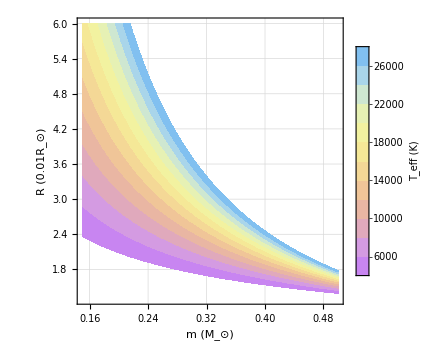

```mathematica
contourprim= ContourPlot[(1.1798232975286564*^47 Log[mmm]^2-1.4023785637137418*^48 Log[mmm] Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]+4.167288525500679*^48 Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]^2)/(7.70388920852663*^43+3.4482434674930335*^44 Log[mmm]+3.858565034251842*^44 Log[mmm]^2) ,{mmm,0.15,0.5},{rr,1.3,6},Contours-> {1,4000,6000,8000,10000,12000,14000,16000,18000,20000,22000,24000,26000,28000},ImageSize-> Medium,ColorFunction->"Pastel", Axes-> True,FrameLabel->{Style["m (M_⊙)",20,Black],Style["R (0.01R_⊙)",20,Black]},FrameTicksStyle->Directive[FontSize->20,Black],ContourStyle->None,ScalingFunctions->{None,None},BaseStyle->{FontSize->20},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["T_eff (K)",Black],LabelStyle->labels],{After,Top}],PlotRange->{{0.15,0.5},{1.3,6},{4000,28000}},LabelStyle->(FontFamily->"Times"),GridLines->Automatic
]
```

```mathematica
cplot1=ContourPlot[(1.1798232975286564*^47 Log[mmm]^2-1.4023785637137418*^48 Log[mmm] Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]+4.167288525500679*^48 Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]^2)/(7.70388920852663*^43+3.4482434674930335*^44 Log[mmm]+3.858565034251842*^44 Log[mmm]^2) ,{mmm,0.15,0.5},{rr,1.3,6},Contours-> {1,4000,6000,8000,10000,12000,14000,16000,18000,20000,22000,24000,26000,28000},ImageSize-> Medium,ColorFunction->"Pastel", Axes-> True,FrameLabel->{Style["m (M_⊙)",Bold,20],Style["R(0.01R_⊙)",Bold,20]},FrameTicksStyle->Directive[FontSize->20],ContourStyle->None,ScalingFunctions->{None,None},LabelStyle->(FontFamily->"Times"),BaseStyle->{FontSize->20},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["T_eff (K)",18],LabelStyle->labels],{After,Top}],PlotRange->{{0.15,0.5},{1.3,3.25},{4000,20000}},BaseStyle->Directive[Opacity[1]]];
```

Now we will make a scatter plot of the measured R, m and T. Taking data compiled from ZTF (Brown et al. 2011; Burdge et al. 2019a,b, 2020a,b)

```mathematica
mtest = {0.32,0.45,0.167,0.32,0.3,0.33,0.38,0.28,0.4,0.36,0.36,0.323,0.335,0.26,1,1,0.27,0.19};
rtest={2.319,2.069,5.70,2.90,2.80,2.49,2.24,2.5,2.2,2.9,2.2,2.98,2.75,3.53,1,1,2.794,5.1};
Ttest = 1000 {12.8,26.45,20,18.25,15.3,16.8,19.9,12,20.4,26,16.5,26,19,16.4,28,4,13.4,16.4};
df2= Transpose[{mtest,rtest,Ttest}];
pts2=df2;
Graphics[{AbsoluteThickness[3],Point[pts2[[All,{1,2}]],VertexColors->ColorData["Pastel"]/@Rescale[pts2[[All,3]]]]},AspectRatio->1,Frame->True];
stylesTemp=ColorData["Pastel"]/@Rescale[pts2[[All,3]]];
Pltfun[ii_]:=ListPlot[{pts2[[All,{1,2}]][[ii]]},PlotRange-> {{0.1,1},{1,6}},AspectRatio->1,PlotMarkers->{"★",18},PlotStyle->{{stylesTemp[[ii]]}},LabelStyle->(FontFamily->"Times"),PlotLegends->{Style["R(m,T_eff) of detached WD",16]}];
```

```mathematica
outline=ListPlot[pts2[[All,{1,2}]],PlotRange-> {{0.1,0.5},{1,6}},AspectRatio->1,PlotMarkers->{"★",24},PlotStyle->{{Black}},PlotLegends->{Style["from Table 1",18]},LabelStyle->(FontFamily->"Times")];
```

```mathematica
outline=ListPlot[pts2[[All,{1,2}]],PlotRange-> {{0.1,0.5},{1,6}},AspectRatio->1,PlotMarkers->{"★",24},PlotStyle->{{Black}},PlotLegends->{Style["from Table 1",18,Bold]},LabelStyle->(FontFamily->"Times")];
```

```mathematica
Show[ListPlot[pts2[[All,{1,2}]],PlotRange-> {{0.9,1.2},{0.5,6}},AspectRatio->1,PlotMarkers->{"★",24},PlotStyle->{{Black}},PlotLegends->{Style["from Table 1",18]},LabelStyle->(FontFamily->"Times")],Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8],Pltfun[9],Pltfun[10],Pltfun[11],Pltfun[12],Pltfun[13],Pltfun[14],Pltfun[15],Pltfun[16],Pltfun[17],Pltfun[18]];
```

We also define the "cold" white dwarf mass radius relation for completely degenerate white dwarfs from Verbunt & Rappaport 1998

```mathematica
Regg[m_]:=0.0114 ((m/1.44)^(-2/3)-(m/1.44)^(2/3))^(1/2)(1+3.5(m/(5.7 10^-4))^(-2/3)+((5.7 10^-4)/m))^(-2/3)
```

```mathematica
plotegg =Plot[100Regg[m],{m,0.15,0.5},AspectRatio->1,AxesLabel-> {Style["mass (solar)",16],Style["radius (solar)",16]},BaseStyle->{FontSize->15},LabelStyle->(FontFamily->"Times"),PlotStyle->{Black,Thick},PlotRange-> {{0.15,0.5},{100 0.013,100 0.06}},PlotLegends->{Style["R(m)",16,Italic]},FrameLabel-> {Style["m_i (M_⊙)",16],Style["R_i (R_⊙)",16],Style["White dwarf masses and radii",Bold,16], Style["R_i (10^8cm)",16]},BaseStyle->{FontSize->15},LabelStyle->(FontFamily->"Times"),Frame-> True,FrameTicks->{{{.1,.2,.3,.4,.5},{Automatic},ChartingScaledTicks[{#/(Rsol/10^8)&,Rsol/10^8#&}]}}];
```

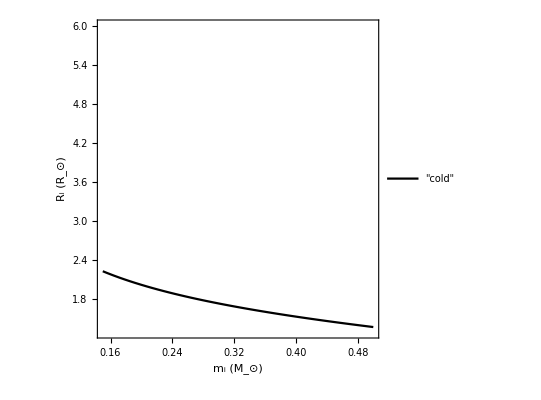

```mathematica
Plot[100Regg[m],{m,0.15,0.5},AspectRatio->1,AxesLabel-> {Style["mass (solar)",16],Style["radius (solar)",16]},BaseStyle->{FontSize->15},LabelStyle->(FontFamily->"Times"),PlotStyle->{Black,Thick},PlotRange-> {{0.15,0.5},{100 0.013,100 0.06}},PlotLegends->{Style[" \"cold\" ",16]},FrameLabel-> {Style["m_i (M_⊙)",16],Style["R_i (R_⊙)",16],Style["White dwarf masses and radii",Bold,16]},BaseStyle->{FontSize->15},LabelStyle->(FontFamily->"Times"),Frame-> True,FrameTicks->{{{.1,.2,.3,.4,.5},{Automatic},ChartingScaledTicks[{#/(Rsol/10^8)&,Rsol/10^8#&}]}}]
```

```mathematica
contourprimempty= ContourPlot[0(1.1798232975286564*^47 Log[mmm]^2-1.4023785637137418*^48 Log[mmm] Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]+4.167288525500679*^48 Log[0.74269870382108113407122043463241581874`15.954589770191005 rr]^2)/(7.70388920852663*^43+3.4482434674930335*^44 Log[mmm]+3.858565034251842*^44 Log[mmm]^2) ,{mmm,0.15,0.5},{rr,1.3,6},Contours-> {1,4000,6000,8000,10000,12000,14000,16000,18000,20000,22000,24000,26000,28000},ImageSize-> Medium,ColorFunction->"Pastel", Axes-> True,FrameLabel->{Style["m (M_⊙)",Bold,20],Style["R (0.01R_⊙)",Bold,20]},FrameTicksStyle->Directive[FontSize->20],ContourStyle->None,ScalingFunctions->{None,None},BaseStyle->{FontSize->20},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["T_eff (K)",Bold],LabelStyle->labels],{After,Top}],PlotRange->{{0.15,0.5},{1.3,6},{4000,28000}},LabelStyle->(FontFamily->"Times")
];
```

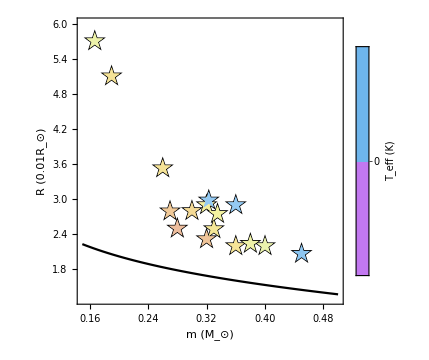

```mathematica
Show[contourprimempty,plotegg,outline,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8],Pltfun[9],Pltfun[10],Pltfun[11],Pltfun[12],Pltfun[13],Pltfun[14],Pltfun[15],Pltfun[16],Pltfun[17],Pltfun[18]]
```

Putting these all together becomes Figure 1:

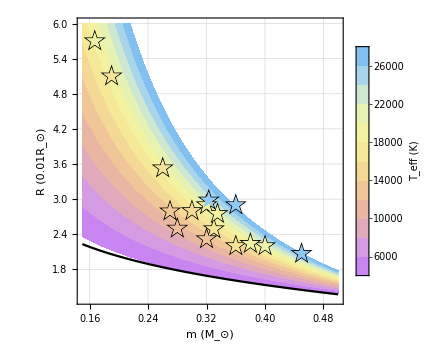

```mathematica
Show[contourprim,plotegg,outline,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8],Pltfun[9],Pltfun[10],Pltfun[11],Pltfun[12],Pltfun[13],Pltfun[14],Pltfun[15],Pltfun[16],Pltfun[17],Pltfun[18]]
```

## Figure 2 : tidal heating vs cooling regime

Using the tidal friction timescale defined in Hut 1981, the gravitational wave frequency f increase due to tidal heating is

```mathematica
fdotTD1[m1_,m2_,fGW_,R1_]=(18 fGW^(13/3)  m2  π^(13/3) R1^5 (fGW/2))/(G^(5/3)m1 (m1+m2)^(5/3))konQ1
```

(1.17044×10^15 fGW^(16/3) konQ1 m2 R1^5)/(m1 (m1+m2)^(5/3))

From gravitational waves the f increase is given by Peters 1964

```mathematica
fdotGW[m1_,m2_,fGW_] = (96 π^(8/3)G^(5/3)(fGW)^(11/3)(Mchirpf[m1,m2])^(5/3))/(5 c^5)//FullSimplify
```

1.83501×10^-62 fGW^(11/3) ((m1 m2)^(3/5)/(m1+m2)^(1/5))^(5/3)

Here we solve for an appropriate k/Q value . Calibrated to Piro 2011.

```mathematica
ratiosol = konQ1/.Solve[fdotTD1[0.26 Msol,0.5 Msol,0.0026,0.0371Rsol] ==0.06 fdotGW[0.26 Msol,0.5 Msol,0.0026] ,konQ1][[1]]
```

7.682×10^-12

For J1539

```mathematica
ratiosol = konQ1/.Solve[fdotTD1[0.21 Msol,0.61 Msol,0.0048,0.0314Rsol] ==0.1 fdotGW[0.21 Msol,0.61 Msol,0.0048] ,konQ1][[1]]
```

7.6605×10^-12

We choose k/Q value:

```mathematica
kQratio =8 10^-12;
```

The fits from Panei et al. 2000 for temperature dependent mass radius relation, defined in McNeill and Hirai 2025 are:

```mathematica
RPanei[m_,T_]:=0.0132 10^(-0.00177 T^(1/2))m^(0.148-0.00941 T^(1/2))
```

```mathematica
Rscale[m1a_,T1a_]:=10^(-0.02792426461145596+0.7641778013995925 √T1a) m1a^(0.14797691065884058-0.9408955042478873 √T1a)
```

```mathematica
WDid = {J0538,J0533,J2029,J0722,J1749,J1901,J2243,J0651,J1539};
m1prims={0.32,0.167,0.32,0.33,0.28,0.36,0.323,0.26,0.21};
T1prims={12.8,20,18.25,16.8,12,26,26.3,16.53,10} 1000;
m2secs={0.45,0.652,0.3,0.38,0.4,0.36,0.335,0.5,0.61};
Porb = {866.6,1233.97,1252.06,1422.55,1586.03,2436.11,528,765,414.8};
fGWs = 2/Porb;
```

The Roche lobe frequency is given by Paczyński 1971

```mathematica
fGWRL=2^(3/2)/(9 π)((G m1prims Msol)/(Rscale[m1prims 10,T1prims/10000]Rsol/100)^3)^(1/2)
```

{0.00971922,0.0016704,0.00780715,0.00879815,0.00789618,0.00812451,0.00610308,0.00539583,0.005439}

White dwarf cooling is given by Mestel 1952, Hurley and Shara 2003:

```mathematica
testZ = 0.02;
Atest=4;
Lsol=3.826 10^33;
Tcold = 4000;
```

```mathematica
L2a[m1_,t_,Z_]:=(300 m1 Z^0.4)/(Atest(t+0.1))^1.18;
```

```mathematica
L2b[m1_,t_,Z_]:=(300(9000 Atest)^5.3 m1 Z^0.4)/(Atest(t+0.1))^6.48;
```

Here we numerically solve the cooling timescale, which is the time from formation to Tcold which we defined as 4000 K .

```mathematica
τcools2=(t/.Table[NSolve[7.1 10^-4(Rsol RPanei[m1prims[[i]],Tcold])^2 Tcold^4==Piecewise[{{L2a[m1prims[[i]],t,testZ],t<9000},{L2b[m1prims[[i]],t,testZ],t>9000}}]Lsol,t],{i,1,9}])//Flatten
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of NSolve::ratnz will be suppressed during this calculation.

{9325.86,3851.99,9325.86,9410.13,8830.64,9652.56,9351.34,7840.16,5564.45}

Then we calculate the tidal friction timescale defined in Hut 1981

```mathematica
τmergeTDfixMyr2 =Table[(2/3 2/18 (( G^(5/3) m1prims[[i]] (m1prims[[i]]Msol+m2secs[[i]] Msol)^(5/3) kQratio^-1)/(fGWs[[i]]^(13/3)  m2secs[[i]] π^(13/3) (Rsol/100 Rscale[m1prims[[i]] 10,T1prims[[i]]/10000])^5)))/(3.15 10^7 10^6),{i,1,9}]
```

{711.981,10.9677,1766.42,4434.85,4887.26,35675.7,18.1169,58.9895,4.58024}

Merger timescale from Peters 1963

The time until Roche contact from present day until Roche lobe frequency (using Paczyński 1971’s)

```mathematica
τRL = Table[Integrate[((96 π^(8/3) G^(5/3))/(5 c^5)(Mchirpf[m1prims[[i]]  Msol,m2secs[[i]]  Msol])^(5/3)f^(11/3))^-1,{f,fGWs[[i]],fGWRL[[i]]}], {i,1,9}]/(3.146 10^7 10^3)
```

{1369.82,374.761,5136.56,5823.65,8590.42,23891.3,339.511,946.937,61.9168}

```mathematica
df1 = Transpose[{-Log10[τmergeTDfixMyr2/τcools2],T1prims,-Log[τRL]}]
```

{{1.11722,12800.,-7.22243},{2.54557,20000,-5.92629},{0.722596,18250.,-8.54414},{0.326716,16800.,-8.66968},{0.256927,12000,-9.0584},{-0.56773,26000,-10.0813},{2.71279,26300.,-5.82751},{2.12355,16530.,-6.85323},{3.08453,10000,-4.12579}}

{{1.11722,12800.,-7.22243},{2.54557,20000,-5.92629},{0.722596,18250.,-8.54414},{0.326716,16800.,-8.66968},{0.256927,12000,-9.0584},{-0.56773,26000,-10.0813},{2.71279,26300.,-5.82751},{2.12355,16530.,-6.85323},{3.08453,10000,-4.12579}}

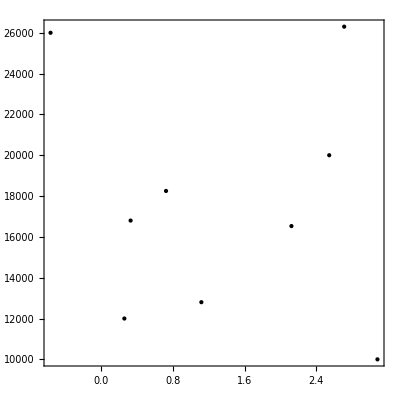

```mathematica
pts2=df1
Graphics[{AbsoluteThickness[3],Point[pts2[[All,{1,2}]],VertexColors->ColorData["Pastel"]/@Rescale[pts2[[All,3]]]]},AspectRatio->1,Frame->True]
```

```mathematica
stylesTemp=ColorData["AvocadoColors"]/@Rescale[pts2[[All,3]]]
```

{RGBColor[0.2662200001907112, 0.6657607184981627, 0.10605701492452253],RGBColor[0.6013843137674506, 0.8003817268070299, 0.1380590176732216],RGBColor[0.00937829904775014, 0.45071129874853755, 0.07602228589411995],RGBColor[0., 0.41987114073143866, 0.07103637307131046],RGBColor[0., 0.3042478657503067, 0.05147451872957574],RGBColor[0., 0., 0.],RGBColor[0.6275689203849568, 0.8100543528554804, 0.14051756276819707],RGBColor[0.3556737798620434, 0.7096159518863118, 0.11498857645020658],RGBColor[1., 0.984375, 0.230411]}

```mathematica
Pltfun[ii_]:=ListPlot[{pts2[[All,{1,2}]][[ii]]},PlotRange-> {{-1.5,4.2},{6000,32000}},AspectRatio->1,PlotMarkers->{"★",18},PlotStyle->{{stylesTemp[[ii]]}},LabelStyle->(FontFamily->"Times")]
```

```mathematica
br2=ListPlot[Transpose[{-Log10[τmergeTDfixMyr2/τcools2],T1prims}],AspectRatio->1,PlotMarkers->{"★",25},PlotStyle->{{Black},"*"},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},PlotRange->{{-1.5,4.2},{6000,32000}},PlotLegends->{Style["Q_1/k_1= 3.5 × 10^9",16]},GridLines->Automatic];
```

```mathematica
labels=Directive[FontSize->18,FontFamily->"Times"];
```

```mathematica
cptrack =ContourPlot[ tscale,{ratio,0,4},{tscale,Min[Log10[τRL]],Max[Log10[τRL]]},Contours-> Table[(i+1)0.1,{i,0,43}],ImageSize-> Medium,ColorFunction->(ColorData["AvocadoColors"]), Axes-> True,FrameTicksStyle->Directive[FontSize->18],ContourStyle->None,ScalingFunctions->{None,None,None},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Log_10(τ_RL in kyr)",18],LabelStyle->labels],{After,Top}],PlotRange->{{0,4},{6000,32000},{2,4.5}},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]",18],Style["T_eff (K)",18]},GridLines->Automatic,FrameStyle->Automatic];
```

```mathematica
cptrack =ContourPlot[ tscale,{ratio,0,4},{tscale,2,5},Contours-> Table[(i+1)0.1,{i,0,43}],ImageSize-> Medium,ColorFunction->(ColorData["AvocadoColors"]), Axes-> True,FrameTicksStyle->Directive[FontSize->18],ContourStyle->None,ScalingFunctions->{None,None,None},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Log_10(τ_RL in kyr)",18],LabelStyle->labels],{After,Top}],PlotRange->{{0,4},{6000,32000},{2.5,4.5}},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]",18],Style["T_eff (K)",18]},GridLines->Automatic,FrameStyle->Automatic];
```

```mathematica
cptrack =ContourPlot[ tscale,{ratio,0,4},{tscale,2.5,4.5},Contours-> Table[(i+1)0.1,{i,0,43}],ImageSize-> Medium,ColorFunction->(ColorData["AvocadoColors"]), Axes-> True,FrameTicksStyle->Directive[FontSize->18,Black],ContourStyle->None,ScalingFunctions->{None,None,None},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->Style["Log_10(τ_RL in kyr)",18],LabelStyle->labels],{After,Top}],PlotRange->{{0-1,3.3},{6000,32000},{2.5,4.5}},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]",18,Black],Style["T_eff (K)",18,Black]},GridLines->Automatic,FrameStyle->Automatic];
```

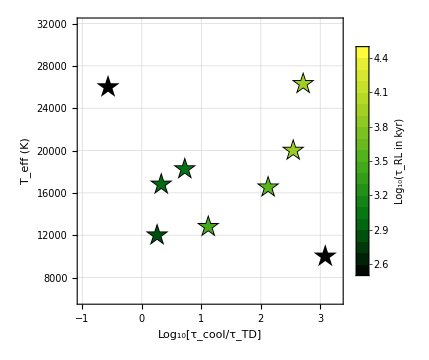

```mathematica
Show[cptrack,br2,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8]]
```

```mathematica
τfricTD =Table[(1/9 (( G^(5/3) m1prims[[i]] (m1prims[[i]]Msol+m2secs[[i]] Msol)^(5/3) kQratio^-1)/(fGWs[[i]]^(13/3)  m2secs[[i]] π^(13/3) (Rsol/100 Rscale[m1prims[[i]] 10,T1prims[[i]]/10000])^5)))/(3.15 10^7 10^6),{i,1,9}]
```

{1067.97,16.4516,2649.62,6652.28,7330.89,53513.5,27.1754,88.4843,6.87036}

```mathematica
τTempTD =Table[(1/9 (( G^(5/3) m1prims[[i]] (m1prims[[i]]Msol+m2secs[[i]] Msol)^(5/3) kQratio^-1)/(fGWs[[i]]^(13/3)  m2secs[[i]] π^(13/3) (Rsol/100 Rscale[m1prims[[i]] 10,T1prims[[i]]/10000])^5)))/(3.15 10^7 10^6),{i,1,9}]
```

{1067.97,16.4516,2649.62,6652.28,7330.89,53513.5,27.1754,88.4843,6.87036}

```mathematica
Log10[τcools2/τfricTD]
```

{0.941129,2.36948,0.546505,0.150625,0.0808355,-0.743821,2.5367,1.94746,2.90844}

```mathematica
br4=ListPlot[Transpose[{-Log10[τfricTD/τcools2],T1prims}],AspectRatio->1,PlotMarkers->{"★",25},PlotStyle->{{Black},"*"},Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["Log_10[τ_cool/τ_TD]"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},PlotRange->{{-1.5,4.2},{6000,32000}},PlotLegends->{Style["Q_1/k_1= 3.5 × 10^9",16]},GridLines->Automatic];
```

```mathematica
τcools2
```

{9325.86,3851.99,9325.86,9410.13,8830.64,9652.56,9351.34,7840.16,5564.45}

```mathematica
list1grey =  Transpose[{{-2,0},{0,0}}];
list2grey =  Transpose[{{-2,0},{400000,400000}}];
```

```mathematica
plotgrey=ListPlot[{list2grey,list1grey},Mesh->All,PlotMarkers->None,Joined->True,Filling->{1->{2}},FillingStyle->{Blend[{Gray,Gray,Black}],Opacity[.3]},PlotStyle-> {{Blend[{Gray,Gray,Black}],Opacity[0.5]}},PlotRange->{{-2,4},{0,222000}},AspectRatio->1,Frame->True,LabelStyle->(FontFamily->"Times"),GridLines->Automatic,PlotLegends->{Style["J0651 primary (Ω_0=0)",16]}];
```

```mathematica
Correlation[-Log10[τmergeTDfixMyr2/τcools2],T1prims]
```

-0.130405

```mathematica
-Log10[τmergeTDfixMyr2/τcools2]
```

{1.11722,2.54557,0.722596,0.326716,0.256927,-0.56773,2.71279,2.12355,3.08453}

Here we calculate the cooling and tidal heating timescales for J1539 in particular .

```mathematica
J1539τ=(2/3 2/18 (( G^(5/3) 0.21 (0.21Msol+0.61 Msol)^(5/3) kQratio^-1)/(0.0048^(13/3)  0.61 π^(13/3) (Rsol/100 Rscale[0.21 10,10000/10000])^5)))/(3.15 10^7 10^6)
```

4.67023

```mathematica
J1539τcool = (t/.NSolve[7.1 10^-4(Rsol RPanei[0.21,Tcold])^2 Tcold^4==Piecewise[{{L2a[0.21,t,testZ],t<9000},{L2b[0.21,t,testZ],t>9000}}]Lsol,t])//Flatten
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{5564.45}

```mathematica
J1539τratio=-Log10[J1539τ/J1539τcool ][[1]]
```

3.07608

```mathematica
J1539temp=10000;
```

```mathematica
(J1539τ/J1539τcool)^-1
```

{1191.47}

```mathematica
mtps=ResourceFunction["PolygonMarker"]["Triangle",{Offset[10],π},{EdgeForm[Blend[{Cyan,Blue,Cyan}]],FaceForm[stylesTemp[[9]]]}];
```

```mathematica
stylesTemp[[8]];
```

```mathematica
J1539plot = ListPlot[{Transpose[{J1539τratio,0.98J1539temp}]},PlotMarkers->{mtps},Joined->False,PlotStyle->{{stylesTemp[[9]]}},PlotRange->{{-1,4},{6000,22000}},AspectRatio->1,Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["f_GW (Hz)"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},GridLines->Automatic,PlotLegends->{Style["J1539 limit",16]}];
```

```mathematica
J1539τratio
```

3.07608

```mathematica
J1539plot = ListPlot[{Transpose[{J1539τratio,0.96J1539temp}]},PlotMarkers->{mtps},Joined->False,PlotStyle->{{stylesTemp[[9]]}},PlotRange->{{-1,3.3},{6000,32000}},AspectRatio->1,Frame->True,LabelStyle->(FontFamily->"Times"),FrameLabel-> {Style["f_GW (Hz)"],Style["T_eff (K)",16]},BaseStyle->{FontSize->16},GridLines->Automatic,PlotLegends->{Style["J1539 limit",16]}];
```

```mathematica
Pltfunwhite[ii_]:=ListPlot[{pts2[[All,{1,2}]][[ii]]},PlotRange-> {{-1.5,4.2},{6000,32000}},AspectRatio->1,PlotMarkers->{"★",40},PlotStyle->{White},LabelStyle->(FontFamily->"Times")]
```

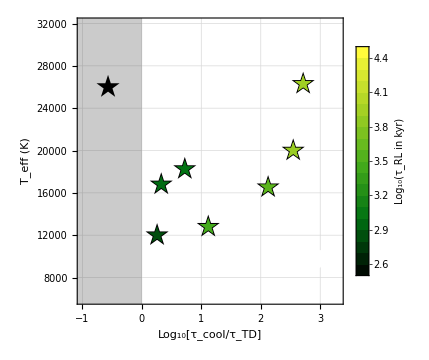

```mathematica
Show[cptrack,plotgrey,br2,J1539plot,Pltfun[1],Pltfun[2],Pltfun[3],Pltfun[4],Pltfun[5],Pltfun[6],Pltfun[7],Pltfun[8],Pltfunwhite[9],J1539plot]
```

## References

Brown, W. R., Kilic, M., Hermes, J. J., et al. 2011, ApJL, 737, L23

Burdge, K. B., Coughlin, M. W., Fuller, J., et al. 2019a, Nature, 571, 528

Burdge, K. B., Fuller, J., Phinney, E. S., et al. 2019b, ApJL, 886, L12

Burdge, K. B., Coughlin, M. W., Fuller, J., et al. 2020a, ApJL, 905, L7 

Burdge, K. B., Prince, T. A., Fuller, J., et al. 2020b, ApJ,905, 32

Hurley, J. R., & Shara, M. M. 2003, ApJ, 589, 179

Hut, P. 1980, A&A, 92, 167

Hut, P. 1981, AAP, 99, 126

Mestel, L. 1952, MNRAS, 112, 583

Paczyński, B. 1971, ARA&A, 9, 183

Panei, J. A., Althaus, L. G., & Benvenuto, O. G. 2000, A&A, 353, 970.

Peters, P. C. 1964, Phys. Rev., 136, B1224

Verbunt, F., & Rappaport, S. 1988, ApJ, 332, 193